```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
(*Calcula os pontos e os pesos da regra de integração *)
IntegrationRule[order_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},
vecPtosPesos=Transpose[GaussianQuadratureWeights[2order,-1,1]];
pts=vecPtosPesos[[1]];
w=vecPtosPesos[[2]];
matpsts=Table[{pts[[j]],pts[[i]],w[[j]] w[[i]] },{i,Length[pts],1,-1},{j,1,Length[pts]}];
matpsts
]
```

```mathematica
(*dado a ordem polinomial gera as funções de forma definidas no elemento mestre -  lineares *)
ComputeShape[order_,var_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
(*list=ListPoli[npoints];
Table[list[[i]],{i,Length[list],1,-1}]*)
ListPoli[npoints]
]
```

```mathematica
(*dado a ordem polinomial gera as funções de forma definidas no elemento mestre -  quadrilátero *)
GeneratePsis[order_]:=Block[{sz,i,j,w,psis,temp,xi,eta},
sz=(2+order-1)(2+order-1);
psis=Table[0,{sz}];
temp=1;
For[i=1,i≤ 1+order,i++,
For[j=1,j≤ 1+order,j++,
psis[[temp]]=(ComputeShape[order,xi][[j]]ComputeShape[order,eta][[i]])*(1);
temp++;
];
];
psis
];
```

```mathematica
(*Calcula as funções psi as coordenas x e y, o gradiente de psi e o jacobiano *)
ComputeData[xis_,etas_,Coords_,order_]:=Block[{psis,GradPhi,x,y,Jac,xi,eta,co,dx,dy},
(*psis=GeneratePsis[order];*)
If[order==1,
psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};

x=Sum[psis[[i]]Coords[[i]][[1]],{i,1,Length[psis]}];
y=Sum[psis[[i]]Coords[[i]][[2]],{i,1,Length[psis]}];

];

If[order==2,
psis={1/4 (xi^2-xi)(eta^2-eta),1/4 (xi^2+xi)(eta^2+eta),1/4 (xi^2+xi)(eta^2-eta),1/4 (xi^2-xi)(eta^2+eta),1/2 (1-xi^2)(1-eta),1/2 (1+xi)(1-eta^2),1/2 (1-xi^2)(1+eta),1/2 (1-xi)(1-eta^2)};

co=Table[0,{8},{2}];
dx=Coords[[2,1]]-Coords[[1,1]];
dy=Coords[[3,2]]-Coords[[2,2]];
co[[1]]=Coords[[1]];
co[[2]]=Coords[[2]];
co[[3]]=Coords[[3]];
co[[4]]=Coords[[4]];
co[[5]]=co[[1]]+dx/2;
co[[6]]=co[[2]]+dy/2;
co[[7]]=co[[3]]-dx/2;
co[[8]]=co[[4]]-dy/2;

x=Sum[psis[[i]]Coords[[i]][[1]],{i,1,Length[psis]}];
y=Sum[psis[[i]]Coords[[i]][[2]],{i,1,Length[psis]}];

];

GradPhi=Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
(*Print["J12 = ",Jac[[1,2]]];*)
{psis,GradPhi,Jac,x,y}/.xi->xis/.eta->etas
]
```

```mathematica
Forcing[x_,y_]:=Block[{},
0
]
```

```mathematica
(*Calcula a contribuição da equação diferencial do problema de elasticidade (ek e ef) em cada ponto de integração *)
ContributeElastic[data_,weight_,order_]:=Block[{C,k,B,fu,InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,ef,x,y,i,j},
nnodes=4 order ;
{psi,GradPsi,Jac,x,y}=data;
(*Print["Jac= ",Jac//MatrixForm];
Print["GradPsi= ",GradPsi//MatrixForm];*)
InvJac=Inverse[Jac];

DetJ=Det[Jac];
(*Print["DetJac = ",DetJ];*)
(*Print["InvJac= ",InvJac//MatrixForm];*)
(*GradPhi=Table[InvJac .GradPsi[[i]],{i,1,Length[GradPsi]}];*)
(*Print["InvJac =",InvJac];
Print["Transpose[GradPsi] =",Transpose[GradPsi]];*)
GradPhi=InvJac.Transpose[GradPsi];
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
(*Print["C = ",C//MatrixForm];*)
wpLocal=weight  DetJ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
fu=-1;
For[i=1,i≤ nnodes,i++,

(*Print["x = ",x];*)
ef[[2i+fu]] +=(Forcing[x,y] psi[[i]])*wpLocal;
ef[[(2*i+1+fu)]]+=(Forcing[x,y] psi[[i]])*wpLocal;
(*ef[[(2*i+fu)]]+=
ef[[(2*i+fu)]]+=
ef[[(2*i+1+fu)]]+=
ef[[(2*i+1+fu)]]+=*)
For[j=1,j≤ nnodes,j++,
ek[[2 i+fu,2j+fu]]+=( GradPhi[[1,i]] C[[1,1]]  GradPhi[[1,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[2,j]])wpLocal ;
ek[[2 i+fu,2j+1+fu]]+=( GradPhi[[1,i]] C[[1,2]]  GradPhi[[2,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
ek[[2 i+1+fu,2j+fu]]+=( GradPhi[[2,i]] C[[1,2]]  GradPhi[[1,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[2,j]])wpLocal ;
ek[[2 i+1+fu,2j+1+fu]]+=( GradPhi[[2,i]] C[[2,2]]  GradPhi[[2,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
];
];
(*Print["ek =",ek//MatrixForm];*)
{ek,ef}
]
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga elementar*)
CalcStiffElastic[order_,elcoords_]:=Block[{Dphi,vecPtosPesos,Dpsi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j,psis,GradPhi,J,DetJ,InvJ,wpLocal,laplacianContribute,L2Contribute,Ex,F,y,f,xi,eta,w,intrule,intpts,l,h,Jac,data},

intrule=IntegrationRule[2order-1];
intpts=Length[intrule];

nnodes=4 order ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

(*Print["intrule =",intrule];
Print["intpts =",intpts];*)
For[l=1,l≤intpts,l++,
For[h=1,h≤ intpts,h++,
xi=intrule[[l,h,1]];
eta=intrule[[l,h,2]];
w=intrule[[l,h,3]];
(*Print["xi = ",xi];
Print["eta = ",eta];*)
data=ComputeData[xi,eta,elcoords,order];
{ek,ef}+=ContributeElastic[data,w,order];

];
];
{ek,ef}
]
```

```mathematica
(*Cria um grid de quadriláteros com nós ordenados no sentido anti-horário*)
CreateRectangularMesh[a_,b_,nx_,ny_]:=Block[{cols,rows,coords,i,j,deltax,deltay,co1,co2,co3,co4,elvec,xstart,ystart,temp},

cols=(nx+2);
rows=(ny+2);
coords=Table[0,{rows},{cols}];

deltax=(b[[1]]-a[[1]])/(nx+1);
deltay=(b[[2]]-a[[2]])/(ny+1);
xstart=a[[1]];
ystart=a[[2]];
temp={0,0};

For[i=1,i≤ rows,i++,
For[j=1,j≤cols,j++,
coords[[i,j]]={xstart,ystart};
xstart+=deltax;
];
ystart+=deltay;
xstart=a[[1]];
];

elvec={};
For[i=1,i<rows,i++,
For[j=1,j<cols,j++,
co1=coords[[i,j]];
co2=coords[[i,j+1]];
co3=coords[[i+1,j]];
co4=coords[[i+1,j+1]];
AppendTo[elvec,{co1,co2,co4 ,co3}];
];
];
elvec
]
```

```mathematica
(*dado uma matriz de coordenadas e elementos, retorna as coordenadas globais ordenadas de acordo com a topologia global*)
ComputeNNodes[RectangularMesh_]:=Block[{allnodes,i,j,alreadcomputednodes,node,newnode,nnodes,y0,nn,firstrow,resto},
allnodes=Flatten[RectangularMesh,1]//N;
y0=allnodes[[1,2]];
(*Print[allnodes];*)
alreadcomputednodes={};
For[i=1,i≤Length[allnodes],i++,
node=allnodes[[i]];
For[j=1+i,j<=Length[allnodes],j++,
If[node==allnodes[[j]], AppendTo[alreadcomputednodes,node]];
];
];
(*Print[alreadcomputednodes];*)
newnode=allnodes;
For[i=1,i<=Length[alreadcomputednodes],i++,
newnode=DeleteCases[newnode,alreadcomputednodes[[i]]];
AppendTo[newnode,alreadcomputednodes[[i]]];

];
nn=newnode;
firstrow={};
resto={};
For[i=1,i≤Length[nn],i++,
If[nn[[i,2]]==y0,
AppendTo[firstrow,nn[[i]]];
,
AppendTo[resto,nn[[i]]];
];
firstrow=SortBy[firstrow,Last];
resto=SortBy[resto,Last];
resto=Sort[resto,#1[[2]]<#2[[2]]&];
];
PrependTo[resto,firstrow];
ArrayReshape[resto,{Length[nn],2}]
];
```

```mathematica
(*Dado uma matriz de coordenadas e elementos retorna a topologia dos elementos *)
ComputeTopol[allnodes_]:=Block[{s,ss,i,j,k,topol,topolvec,topolgeral},
topolvec={};
s=allnodes//N;
ss=ComputeNNodes[s]//N;
topolgeral={};
For[i=1,i≤Length[s],i++,

topol=Table[0,{4}];
For[j=1,j≤4,j++,
For[k=1,k≤Length[ss],k++,
If[s[[i,j]]==ss[[k]],
topol[[j]]=k;
AppendTo[topolgeral,k];
];
];

];
AppendTo[topolvec,topol];

];
topolvec
];
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga globais *)
Assemble[allcoords_,order_,forcing_]:=Block[{fu,nels,p,i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co,nnodes,topol},

p=order;
nels=Length[allcoords];
nnodes=ComputeNNodes[allcoords]//N;
(*Print["Nnodes = ",nnodes];*)
sz=Length[nnodes] 2;
rows=order 4;
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
(*Print["Kglob = ",Kglob//MatrixForm];*)
topol=ComputeTopol[allcoords];
Print["topol = ",topol];
For[k=1,k≤nels,k++,
co=allcoords[[k]]//N;
(*Print["k = ",k];*)
(*Print["co = ",co];*)
{Ke,Fe}=CalcStiffElastic[order,co];
(*Print["Ke = ",Ke//MatrixForm];*)

ik=(k-1)*order 4;
fu=-1;
For[i=1,i≤rows,i++,
rowglob=topol[[k,i]];
For[j=1,j≤cols,j++,
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];

];
Fglob[[2rowglob+fu]]+=Fe[[i]];
];
];
{Kglob,Fglob}
]
```

```mathematica
(*Dada a matriz de rigidez e o vetor de carga globais, aplica condição de contorno definida em nós*)
ApplyNodeBC[Kglob_,Fglob_,node_,type_,ek_,ef_]:=Block[{position,i,j,kglob=Kglob,fglob=Fglob},

If[type≠0&&type≠1 && type≠2,Print["Unknown type. Specify 0 for Dirichlet, 1 for Newman or 2 for Mixed."]];
position=node 2-1;
If[type==0,
(*Dirichlet - Specified Solution *)
For[i=1,i≤2,i++,
For[j=1,j≤2,j++,
kglob[[position+i-1,position+j-1]]*=ek[[i,j]];
];
fglob[[position+i-1]]=ef[[i]];
];
];
If[type==1,

(*Newman - Specified Load*)
For[i=1,i≤2,i++,
fglob[[position+i-1]]+=ef[[i]];
];

];
{kglob,fglob}
]
```

```mathematica
(*Dado dois ids extremos, retorna uma topologia e as coordenas completas intermediárias aos nós de um elemento linear*)
DefineLineNodes[id1_,id2_,nnodes_]:=Block[{A,B,tol,linenodes,i,ids,elss},
A=nnodes[[id1]];
B=nnodes[[id2]];
tol=10^-3;
linenodes={};
ids={};
For[i=1,i≤Length[nnodes],i++,

(*x=x Linha vertical*)
If[Abs[A[[1]]-B[[1]]]<tol && Abs[nnodes[[i]][[1]]-A[[1]]]<tol,

If[Between[nnodes[[i]][[2]],{A[[2]],B[[2]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];

];

(*y=y Linha horizontal*)
If[Abs[A[[2]]-B[[2]]]<tol&& Abs[nnodes[[i]][[2]]-A[[2]]]<tol,
If[Between[nnodes[[i]][[1]],{A[[1]],B[[1]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];
];

];
elss={};
For[i=1,i<Length[ids],i++,

AppendTo[elss,{nnodes[[ ids[[i]] ]],nnodes[[ ids[[i+1]] ]]} ];

];

{elss,ids}
];
```

```mathematica
(*dado duas coordenas e a ordem de interpolação divide a linha no número de dós necessários*)
ComputeNewLinearNodes[order_,coords_]:=Block[{xa,xb,newcoords},
xa=coords[[1]];
xb=coords[[2]];
newcoords=Table[xa+(1-i)(xa-xb)/order,{i,1,order+1}];
newcoords
]
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLine[EK_,EF_,fx_,order_,nodes_,id1_,id2_]:=Block[{els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco},


{els,ids}=DefineLineNodes[id1,id2,nodes];
el=Length[els];
For[i=1,i≤el,i++,
shapes=ComputeShape[order,xi];
co={els[[i]][[1,1]],els[[i]][[2,1]]};
newco=ComputeNewLinearNodes[order,co];
xx=Sum[shapes[[i]] newco[[i]],{i,1,order+1}];
J=D[xx,xi];
vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((fx[xx]shapes[[j]])/.xi->xix[[i]]) w[[i]]J,{i,1,Length[xix]}],{j,1,Length[shapes]}];
Print["Fi = ",integralxi1];
];

]
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLineNewman[EF_,fx_,order_,nodes_,id1_,id2_,fxorfy_]:=Block[{Ef=EF,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco},

{els,ids}=DefineLineNodes[id1,id2,nodes];
el=Length[els];
For[i=1,i≤el,i++,
shapes=ComputeShape[order,xi];

If[fxorfy==1,(*fy*)
co={els[[i]][[1,1]],els[[i]][[2,1]]};
Print["co = ",co];
,
(*fx*)
co={els[[i]][[1,2]],els[[i]][[2,2]]};
];

Print["Co = ",co];
newco=co;
(*newco=ComputeNewLinearNodes[order,co];*)
xx=Sum[shapes[[i]] newco[[i]],{i,1,order+1}];
J=D[xx,xi];
vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((fx[xx]shapes[[j]])/.xi->xix[[i]]) w[[i]]J,{i,1,Length[xix]}],{j,1,Length[shapes]}];
Print["ids[[i]] = ",ids[[i]]];
If[fxorfy==1,(*fy*)
Ef[[ ids[[i]] 2]]+=integralxi1[[1]];
Ef[[ ids[[i+1]] 2]]+=integralxi1[[2]];
,
(*fx*)
Ef[[ ids[[i]]2-1 ]]+=integralxi1[[1]];
Ef[[ ids[[i]]2 ]]+=integralxi1[[2]];
];
];
Ef
];
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLineDirichlet[EK_,EF_,nodes_,id1_,id2_,ek_,ef_]:=Block[{Ef=EF,Ek=EK,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,k},

{els,ids}=DefineLineNodes[id1,id2,nodes];
el=Length[els];

For[i=1,i≤el+1,i++,

For[j=1,j≤2,j++,
For[k=1,k≤2,k++,

Ek[[2ids[[i]] +j-2,2ids[[i]]+k-2 ]]*=ek[[j,k]];
];
Ef[[2ids[[i]] +j-2]]=ef[[j]];
];


];
{Ek,Ef}
];
```

```mathematica
(*Calcula a solução e a derivada definida por elementos *)
ComputeSol[topol_,coords_,order_,coefs_]:=Block[{nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac},

psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
nels=Length[topol];
sol=Table[0,{nels},{2}];
dsol=Table[0,{nels},{4}];
For[i=1,i≤nels,i++,

x=0.;
y=0.;

For[j=1,j≤4,j++,
id=topol[[i,j]];
x+=coords[[id,1]] psis[[j]];
y+=coords[[id,2]] psis[[j]];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
DetJac=Det[Jac];
];

For[j=1,j≤4,j++,
id=topol[[i,j]];
sol[[i,1]]+=(psis[[j]] coefs[[2 id-1]] DetJac);
sol[[i,2]]+=(psis[[j]] coefs[[2id]] DetJac);

(*duxdx*)
dsol[[i,1]]+=(D[psis[[j]],xi] coefs[[2 id-1]] DetJac);
(*duxdy*)
dsol[[i,2]]+=(D[psis[[j]],eta] coefs[[2id-1]] DetJac);
(*duydx*)
dsol[[i,3]]+=(D[psis[[j]],xi] coefs[[2id]] DetJac);
(*duydy*)
dsol[[i,4]]+=(D[psis[[j]],eta] coefs[[2id]] DetJac);
(*Print["j+k = ",j+k];
Print["j = ",j];*)
];

];
{sol,dsol}
]
```

```mathematica
(*Calcula as tensões nos elementos*)
ComputeStress[dsol_,young_,nu_]:=Block[{gradu,lambda=young nu/((1+nu)(1-2 nu)),mu=young/(2(1+nu)),dudx,dudy,dvdx,dvdy,i,eps,stress,ex,ey,exy,C},

eps=Table[0,{Length[dsol]}];
stress=Table[0,{Length[dsol]}];
For[i=1,i≤Length[dsol],i++,

{dudx,dudy,dvdx,dvdy}=dsol[[i]];
(*If[i==1,Print["{dudx,dudy,dvdx,dvdy} = ",{dudx,dudy,dvdx,dvdy}]];*)
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
stress[[i]]=C.{ex,ey,exy};
(*gradu={{dudx,dudy},{dvdx,dvdy}};
eps[[i]]=(gradu+Transpose[gradu])/2;
stress[[i]]=lambda Tr[eps[[i]]]IdentityMatrix[2]+2 mu eps[[i]];*)

];
{stress,eps}
];
```

{{{2,1},{5,2},{4,6},{1,4}}}

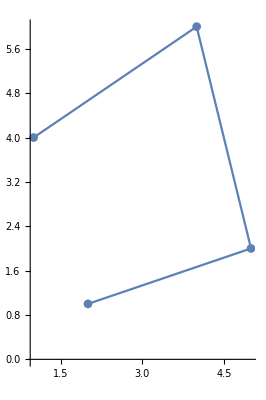

topol = {{1,2,4,3}}

KE = (0.407005 | 0.104972 | -0.300742 | -0.139621 | -0.0160288 | 0.150145 | -0.0902343 | -0.115496
0.104972 | 0.545515 | -0.0729543 | -0.0286192 | 0.0834783 | -0.239883 | -0.115496 | -0.277013
-0.300742 | -0.0729543 | 0.702964 | -0.142679 | -0.454073 | 0.13441 | 0.0518507 | 0.0812231
-0.139621 | -0.0286192 | -0.142679 | 0.393915 | 0.13441 | -0.182949 | 0.14789 | -0.182347
-0.0160288 | 0.0834783 | -0.454073 | 0.13441 | 0.748217 | -0.144182 | -0.278116 | -0.073706
0.150145 | -0.239883 | 0.13441 | -0.182949 | -0.144182 | 0.432273 | -0.140373 | -0.00944048
-0.0902343 | -0.115496 | 0.0518507 | 0.14789 | -0.278116 | -0.140373 | 0.316499 | 0.107979
-0.115496 | -0.277013 | 0.0812231 | -0.182347 | -0.073706 | -0.00944048 | 0.107979 | 0.4688)

FE = (0.
0
0.
0
0.
0
0.
0)

```mathematica
order=1;
young=1;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{2,1},{5,2},{4,6},{1,4}}}
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,Joined->True]
{KE,FE}=Assemble[allcoords,1,1];

Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]
```

topol = {{1,2,9,10},{2,3,8,9},{3,4,7,8},{4,5,6,7},{10,9,14,15},{9,8,13,14},{8,7,12,13},{7,6,11,12}}

co = {8.,6.}

Co = {8.,6.}

ids[[i]] = 11

co = {6.,4.}

Co = {6.,4.}

ids[[i]] = 12

co = {4.,2.}

Co = {4.,2.}

ids[[i]] = 13

co = {2.,0.}

Co = {2.,0.}

ids[[i]] = 14

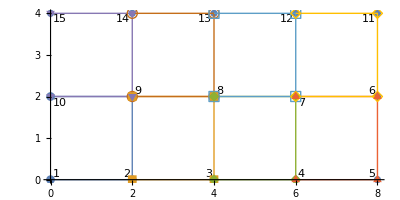

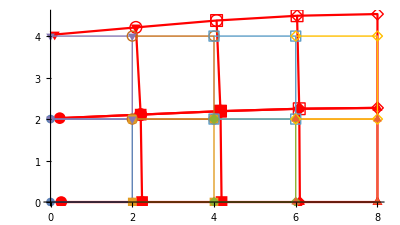

{-0.591224,24.0375,0.938379}

{0.591224,22.1064,1.11527}

{-2.75303,54.8451,1.58273}

{2.75303,54.6533,2.56726}

{-5.20869,80.6199,1.2421}

{5.20869,81.6118,1.77231}

{-6.57035,95.144,0.430147}

{6.57035,96.2749,0.604849}

```mathematica
order=1;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords=CreateRectangularMesh[{0,0},{8,4},3,1];

nnodes=ComputeNNodes[allcoords]//N;
{KE,FE}=Assemble[allcoords,1,1];
newkt=KE;
KEt=KE;

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,5,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,5,11,{{10^12,1},{1,1}},{0,0}];


q=100;
L=16;
f[x_]:=-q Sin[Pi x/L];
diry=1;
FE=ContributeLineNewman[FE,f,1,nnodes,15,11,diry];
dirx=0;
(*FE=ContributeLineNewman[FE,f,1,nnodes,5,11,dirx];*)



sol=LinearSolve[KE,FE,Method->"Cholesky"];
scale=40000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]


defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
topol=ComputeTopol[allcoords];
solels=ComputeSol[topol,nnodes,1,sol];
stress=ComputeStress[solels[[2]],30 10^6,0.30][[1]];
stress[[1]]/.{xi->0,eta->0}
stress[[5]]/.{xi->0,eta->0}
stress[[2]]/.{xi->0,eta->0}
stress[[6]]/.{xi->0,eta->0}
stress[[3]]/.{xi->0,eta->0}
stress[[7]]/.{xi->0,eta->0}
stress[[4]]/.{xi->0,eta->0}
stress[[8]]/.{xi->0,eta->0}
```

```mathematica
sol[[1]]
sol[[2]]
```

6.57508×10^-6

1.1517×10^-18

```mathematica
sol[[9 2-1]]
sol[[9 2]]
```

5.15385×10^-6

2.67804×10^-6

topol = {{1,2,19,20},{2,3,18,19},{3,4,17,18},{4,5,16,17},{5,6,15,16},{6,7,14,15},{7,8,13,14},{8,9,12,13},{9,10,11,12},{20,19,29,30},{19,18,28,29},{18,17,27,28},{17,16,26,27},{16,15,25,26},{15,14,24,25},{14,13,23,24},{13,12,22,23},{12,11,21,22},{30,29,39,40},{29,28,38,39},{28,27,37,38},{27,26,36,37},{26,25,35,36},{25,24,34,35},{24,23,33,34},{23,22,32,33},{22,21,31,32}}

co = {8.,7.11111}

Co = {8.,7.11111}

ids[[i]] = 31

co = {7.11111,6.22222}

Co = {7.11111,6.22222}

ids[[i]] = 32

co = {6.22222,5.33333}

Co = {6.22222,5.33333}

ids[[i]] = 33

co = {5.33333,4.44444}

Co = {5.33333,4.44444}

ids[[i]] = 34

co = {4.44444,3.55556}

Co = {4.44444,3.55556}

ids[[i]] = 35

co = {3.55556,2.66667}

Co = {3.55556,2.66667}

ids[[i]] = 36

co = {2.66667,1.77778}

Co = {2.66667,1.77778}

ids[[i]] = 37

co = {1.77778,0.888889}

Co = {1.77778,0.888889}

ids[[i]] = 38

co = {0.888889,0.}

Co = {0.888889,0.}

ids[[i]] = 39

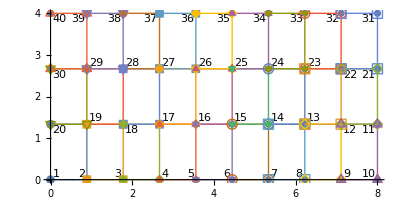

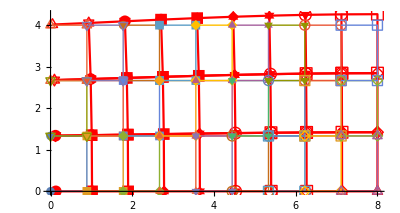

```mathematica
allcoords=CreateRectangularMesh[{0,0},{8,4},8,2];
nnodes=ComputeNNodes[allcoords]//N;
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];


order=1;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));

{KE,FE}=Assemble[allcoords,1,1];
newkt=KE;
KEt=KE;

{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,10,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,10,31,{{10^12,1},{1,1}},{0,0}];


q=100;
L=16;
f[x_]:=-q Sin[Pi x/L];
diry=1;
FE=ContributeLineNewman[FE,f,1,nnodes,40,31,diry];
dirx=0;
(*FE=ContributeLineNewman[FE,f,1,nnodes,5,11,dirx];*)



sol=LinearSolve[KE,FE,Method->"Cholesky"];
scale=20000;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];
nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]
defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
```

```mathematica
30 10^6
```

30000000

-Graphics3D-

topol = {{1,2,21,22},{2,3,20,21},{3,4,19,20},{4,5,18,19},{5,6,17,18},{6,7,16,17},{7,8,15,16},{8,9,14,15},{9,10,13,14},{10,11,12,13},{22,21,32,33},{21,20,31,32},{20,19,30,31},{19,18,29,30},{18,17,28,29},{17,16,27,28},{16,15,26,27},{15,14,25,26},{14,13,24,25},{13,12,23,24},{33,32,43,44},{32,31,42,43},{31,30,41,42},{30,29,40,41},{29,28,39,40},{28,27,38,39},{27,26,37,38},{26,25,36,37},{25,24,35,36},{24,23,34,35},{44,43,54,55},{43,42,53,54},{42,41,52,53},{41,40,51,52},{40,39,50,51},{39,38,49,50},{38,37,48,49},{37,36,47,48},{36,35,46,47},{35,34,45,46},{55,54,65,66},{54,53,64,65},{53,52,63,64},{52,51,62,63},{51,50,61,62},{50,49,60,61},{49,48,59,60},{48,47,58,59},{47,46,57,58},{46,45,56,57},{66,65,76,77},{65,64,75,76},{64,63,74,75},{63,62,73,74},{62,61,72,73},{61,60,71,72},{60,59,70,71},{59,58,69,70},{58,57,68,69},{57,56,67,68},{77,76,87,88},{76,75,86,87},{75,74,85,86},{74,73,84,85},{73,72,83,84},{72,71,82,83},{71,70,81,82},{70,69,80,81},{69,68,79,80},{68,67,78,79},{88,87,98,99},{87,86,97,98},{86,85,96,97},{85,84,95,96},{84,83,94,95},{83,82,93,94},{82,81,92,93},{81,80,91,92},{80,79,90,91},{79,78,89,90},{99,98,109,110},{98,97,108,109},{97,96,107,108},{96,95,106,107},{95,94,105,106},{94,93,104,105},{93,92,103,104},{92,91,102,103},{91,90,101,102},{90,89,100,101},{110,109,120,121},{109,108,119,120},{108,107,118,119},{107,106,117,118},{106,105,116,117},{105,104,115,116},{104,103,114,115},{103,102,113,114},{102,101,112,113},{101,100,111,112}}

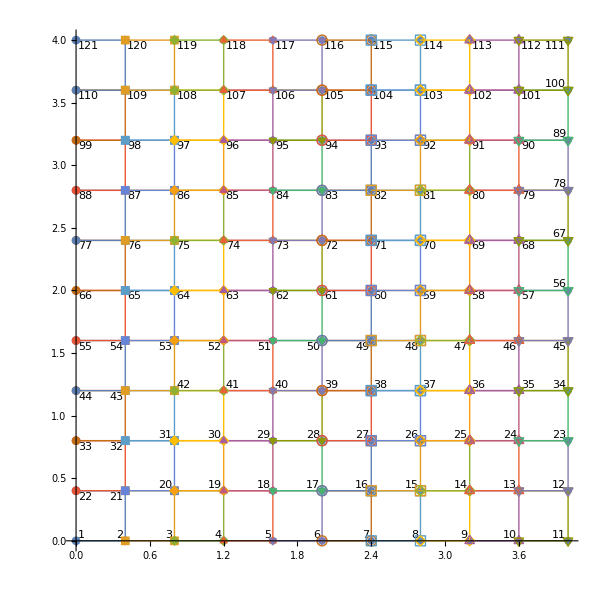

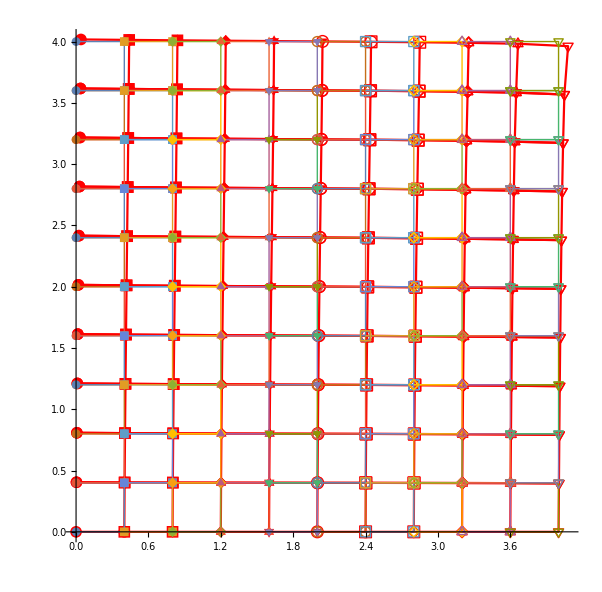

```mathematica
order=1;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
Forcing[x_,y_]:=Block[{},
(*10(4-x)(0-x)(4-y)(0-y)*)
0
]
Plot3D[Forcing[x,y],{x,0,4},{y,0,4}]

allcoords=CreateRectangularMesh[{0,0},{4,4},9,9];
undefplot=ListLinePlot[allcoords,AspectRatio->Automatic,PlotMarkers->Automatic,Joined->True];
nnodes=ComputeNNodes[allcoords]//N;
{KE,FE}=Assemble[allcoords,1,1];

(*(*Dirichlet - vy=0 vy=0 no no 1*)
{KE,FE}=ApplyNodeBC[KE,FE,1,0,{{10^12,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,11,0,{{10^12,1},{1,10^12}},{0,0}];*)


{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,11,{{10^12,1},{1,10^12}},{0,0}];

(*Newman - fx=10000 no no 111*)
{KE,FE}=ApplyNodeBC[KE,FE,111,1,{{1,1},{1,1}},{10000,0}];
(*Print["FE = ",FE//MatrixForm]*)
(*f[x_]:=20000;

dirx=0;
FE=ContributeLineNewman[FE,f,1,nnodes,11,111,dirx];*)
(*Print["FE = ",FE//MatrixForm]*)
(*Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]*)

sol=LinearSolve[KE,FE,Method->"Cholesky"];
scale=20;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];


nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]
defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
```

```mathematica
4/10.
```

0.4

```mathematica
sol[[111 2 -1]]
sol[[111 2]]
```

0.00394683

-0.00186717

```mathematica
sol[[121 2-1]]
sol[[121 2]]
```

0.00202266

0.000863117

```mathematica
22 0.27475E-02
```

14.4307

```mathematica
Max[sol]
```

0.00394683

-Graphics3D-

topol = {{1,2,21,22},{2,3,20,21},{3,4,19,20},{4,5,18,19},{5,6,17,18},{6,7,16,17},{7,8,15,16},{8,9,14,15},{9,10,13,14},{10,11,12,13},{22,21,32,33},{21,20,31,32},{20,19,30,31},{19,18,29,30},{18,17,28,29},{17,16,27,28},{16,15,26,27},{15,14,25,26},{14,13,24,25},{13,12,23,24},{33,32,43,44},{32,31,42,43},{31,30,41,42},{30,29,40,41},{29,28,39,40},{28,27,38,39},{27,26,37,38},{26,25,36,37},{25,24,35,36},{24,23,34,35},{44,43,54,55},{43,42,53,54},{42,41,52,53},{41,40,51,52},{40,39,50,51},{39,38,49,50},{38,37,48,49},{37,36,47,48},{36,35,46,47},{35,34,45,46},{55,54,65,66},{54,53,64,65},{53,52,63,64},{52,51,62,63},{51,50,61,62},{50,49,60,61},{49,48,59,60},{48,47,58,59},{47,46,57,58},{46,45,56,57},{66,65,76,77},{65,64,75,76},{64,63,74,75},{63,62,73,74},{62,61,72,73},{61,60,71,72},{60,59,70,71},{59,58,69,70},{58,57,68,69},{57,56,67,68},{77,76,87,88},{76,75,86,87},{75,74,85,86},{74,73,84,85},{73,72,83,84},{72,71,82,83},{71,70,81,82},{70,69,80,81},{69,68,79,80},{68,67,78,79},{88,87,98,99},{87,86,97,98},{86,85,96,97},{85,84,95,96},{84,83,94,95},{83,82,93,94},{82,81,92,93},{81,80,91,92},{80,79,90,91},{79,78,89,90},{99,98,109,110},{98,97,108,109},{97,96,107,108},{96,95,106,107},{95,94,105,106},{94,93,104,105},{93,92,103,104},{92,91,102,103},{91,90,101,102},{90,89,100,101},{110,109,120,121},{109,108,119,120},{108,107,118,119},{107,106,117,118},{106,105,116,117},{105,104,115,116},{104,103,114,115},{103,102,113,114},{102,101,112,113},{101,100,111,112}}

Co = {0.,0.4}

ids[[i]] = 11

Co = {0.4,0.8}

ids[[i]] = 12

Co = {0.8,1.2}

ids[[i]] = 23

Co = {1.2,1.6}

ids[[i]] = 34

Co = {1.6,2.}

ids[[i]] = 45

Co = {2.,2.4}

ids[[i]] = 56

Co = {2.4,2.8}

ids[[i]] = 67

Co = {2.8,3.2}

ids[[i]] = 78

Co = {3.2,3.6}

ids[[i]] = 89

Co = {3.6,4.}

ids[[i]] = 100

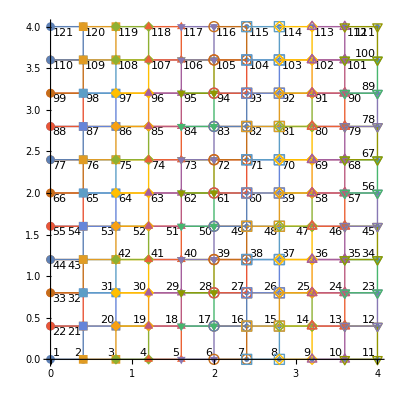

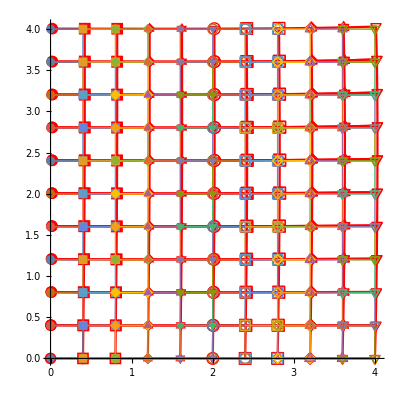

```mathematica
order=1;
young=30 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
Forcing[x_,y_]:=Block[{},
(*10(4-x)(0-x)(4-y)(0-y)*)
0
]
Plot3D[Forcing[x,y],{x,0,4},{y,0,4}]

allcoords=CreateRectangularMesh[{0,0},{4,4},9,9];
undefplot=ListLinePlot[allcoords,AspectRatio->Automatic,PlotMarkers->Automatic,Joined->True];
nnodes=ComputeNNodes[allcoords]//N;
{KE,FE}=Assemble[allcoords,1,1];

(*(*Dirichlet - vy=0 vy=0 no no 1*)
{KE,FE}=ApplyNodeBC[KE,FE,1,0,{{10^12,1},{1,10^12}},{0,0}];

(*Dirichlet -  vy=0 no no 2*)
{KE,FE}=ApplyNodeBC[KE,FE,11,0,{{10^12,1},{1,10^12}},{0,0}];*)


{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,1,11,{{10^12,1},{1,10^12}},{0,0}];

(*Newman - fx=10000 no no 111*)
(*{KE,FE}=ApplyNodeBC[KE,FE,111,1,{{1,1},{1,1}},{10000,0}];*)
(*Print["FE = ",FE//MatrixForm]*)
f[x_]:=20000;

dirx=0;
FE=ContributeLineNewman[FE,f,1,nnodes,11,111,dirx];
(*Print["FE = ",FE//MatrixForm]*)
(*Print["KE = ",KE//MatrixForm]
Print["FE = ",FE//MatrixForm]*)
(*dirx=1;
FE=ContributeLineNewman[FE,f,1,nnodes,121,111,dirx];*)


sol=LinearSolve[KE,FE,Method->"Cholesky"];
scale=20;
deformed=(Flatten[nnodes]+scale sol);

tabdeformed=Table[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];

nf=Nearest[tabdeformed];

tabdeformed2=ArrayReshape[#,Dimensions@allcoords]&@Flatten[nf@Flatten[allcoords,1],1];


nodeids=ListPlot[Table[Labeled[nnodes[[i]],i],{i,Length@nnodes}],AspectRatio->Automatic];
undefplot=ListLinePlot[Tooltip[allcoords],AspectRatio->Automatic,PlotMarkers->Automatic,PlotStyle->{Thick}];
Show[nodeids,undefplot]
defplot=ListLinePlot[Tooltip[tabdeformed2],AspectRatio->Automatic,PlotMarkers->{Automatic,12},PlotStyle->{Red}];
Show[defplot,undefplot,PlotRange->All]
```